## Scientific Programming 2

First steps in working with expressions

### Parts of expressions

Everything in Mathematica is an expression. 
Expressions have the form Head[e1,e2,...].
The simplest types of expressions are Integers, Reals, Rationals, Complex or List.

```mathematica
ls={a,b,c,d,e,f,g,h,i,j,k};
```

Mathematica lists are indexed beginning with 1. In C and other common programming languages, arrays are indexed starting with 0.
In Mathematica, the 0-th component of the list is reserved for the "head". The head gives much information about the type of expression in question.

```mathematica
ls⟦0⟧
```

List

```mathematica
Length[ls]
```

11

```mathematica
Part[ls,1]
```

a

```mathematica
ls⟦1⟧
```

a

```mathematica
?Part
```

```mathematica
ls⟦2;;7⟧ (*elements from 2 to 7*)
```

{b,c,d,e,f,g}

```mathematica
ls⟦2;;8;;2⟧ (*elements from 2 to 8 in steps of 2*)
```

{b,d,f,h}

```mathematica
ls⟦-1⟧ (*-1 counts from the end*)
```

k

```mathematica
ls⟦-3⟧
```

i

```mathematica
First[ls]
```

a

```mathematica
Rest[ls]
```

{b,c,d,e,f,g,h,i,j,k}

```mathematica
Last[ls]
```

k

```mathematica
Take[ls,5](*1st 5 elements*)
```

{a,b,c,d,e}

```mathematica
Take[ls,2;;8;;2]
```

{b,d,f,h}

```mathematica
Take[ls,{5,7}]
```

{e,f,g}

```mathematica
Drop[ls,5] (*last five elements*)
```

{f,g,h,i,j,k}

```mathematica
ReplacePart[ls,3->x]
```

{a,b,x,d,e,f,g,h,i,j,k}

```mathematica
expr=a+f[x,y^n];
```

```mathematica
FullForm[expr]
```

Plus[a,f[x,Power[y,n]]]

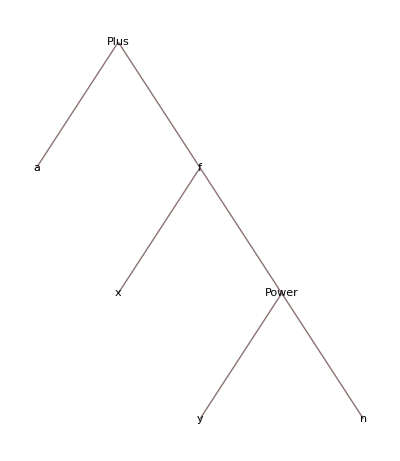

```mathematica
TreeForm[expr]
```

```mathematica
Depth[expr]
```

4

```mathematica
Level[expr,1]
```

{a,f[x,y^n]}

```mathematica
Level[expr,2] (*everything up to level 2*)
```

{a,x,y^n,f[x,y^n]}

```mathematica
Level[expr,3]
```

{a,x,y,n,y^n,f[x,y^n]}

```mathematica
expr[[0]](*head of expr*)
```

Plus

```mathematica
expr[[2,2,0]]
```

Power

```mathematica
ReplacePart[expr,{2,2,0}->Plus]
```

a+f[x,n+y]

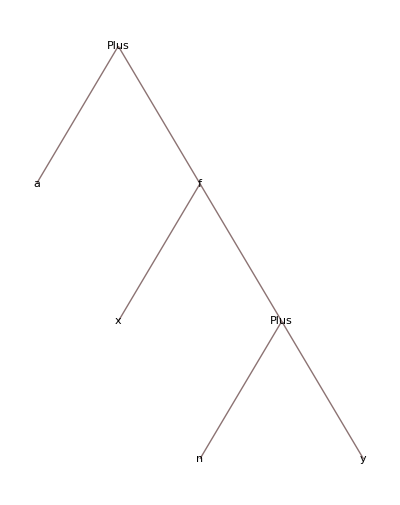

```mathematica
TreeForm[%]
```

### Pure Functions

Pure function with one argument :

```mathematica
Function[u,3+u][x]
```

3+x

```mathematica
Function[3+#][x](*Recall # is a dummy*)
```

3+x

```mathematica
(3+#)&[x] (*Whatever is before & is the function definition*)
```

3+x

```mathematica
g=(#+3)&;

g[x]
```

3+x

```mathematica
FullForm[g]
```

Function[Plus[Slot[1],3]]

```mathematica
f[u_]:=u+3

f[x]
```

3+x

```mathematica
Head[f]
```

Symbol

```mathematica
Head[g]
```

Function

The expressions f and g can both be used as "functions".  However, they are different. f is recognised by Mathematica as a Symbol, for which the rule f[x_] := x + 3 has been associated.
    On the other hand, g is recognised a Function, i.e. a pure function.  There are situations when a pure function is required, such as selecting parts of expressions with functions.

Pure function with two arguments:

```mathematica
Function[{u,v},u^2+v^4][x,y]
```

x^2+y^4

```mathematica
Function[#1^2+#2^4][x,y]
```

x^2+y^4

```mathematica
(#1^2+#2^4)&[x,y]
```

x^2+y^4

```mathematica
Function[{x,y},x+y][{1,2},2](*{1,2} are the arguments of x *)
```

{3,4}

```mathematica
Clear[f,g];
```

```mathematica
ls
```

{a,b,c,d,e,f,g,h,i,j,k}

```mathematica
Select[ls,(#==a)&] (*Selects all elements that satisfy the criterion*)
```

{a}

### Map and Apply

Map[F, expr] applies F to each element on the first level in expr

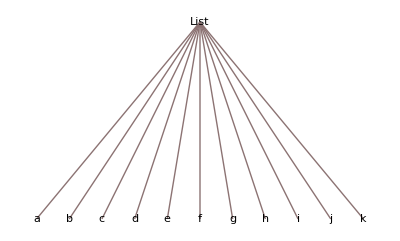

```mathematica
TreeForm[ls]
```

```mathematica
Map[F,ls]
```

{F[a],F[b],F[c],F[d],F[e],F[f],F[g],F[h],F[i],F[j],F[k]}

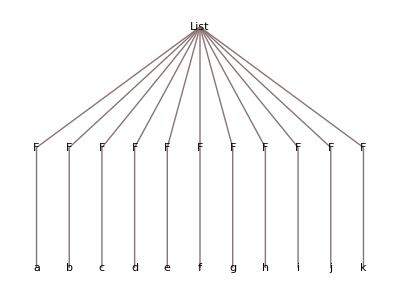

```mathematica
TreeForm[Map[F,ls]]
```

```mathematica
F/@ls (*This is the same as Map[F,ls]*)
```

{F[a],F[b],F[c],F[d],F[e],F[f],F[g],F[h],F[i],F[j],F[k]}

```mathematica
F@x (*Note that if we don't use the /, then we act on the whole list*)
```

F[x]

An expression does not have to be a list

```mathematica
g[a,b,c]//FullForm
```

g[a,b,c]

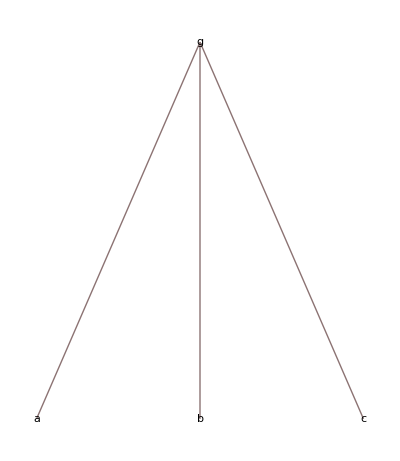

```mathematica
TreeForm[g[a,b,c]]
```

```mathematica
Head[%]
```

g

```mathematica
f/@g[a,b,c]
```

g[f[a],f[b],f[c]]

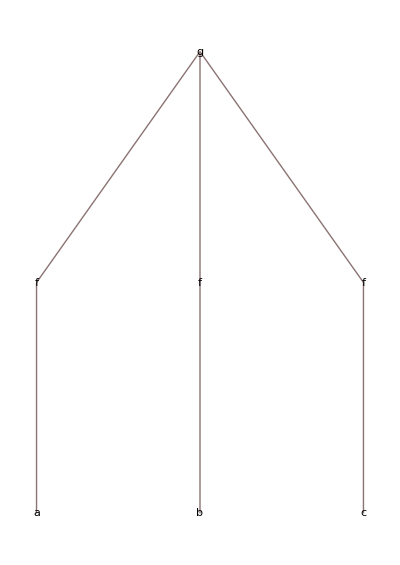

```mathematica
TreeForm[f/@g[a,b,c]]
```

Some functions are Listable (they automatically distribute themselves to the list)

```mathematica
Log/@ls
```

{Log[a],Log[b],Log[c],Log[d],Log[e],Log[f],Log[g],Log[h],Log[i],Log[j],Log[k]}

```mathematica
Log[ls]
```

{Log[a],Log[b],Log[c],Log[d],Log[e],Log[f],Log[g],Log[h],Log[i],Log[j],Log[k]}

```mathematica
Attributes[Log]
```

{Listable,NumericFunction,Protected}

```mathematica
SetAttributes[h, Listable] (*Can set the attributes of h to be listable!*)
```

```mathematica
?h
```

Global`h

Attributes[h]={Listable}

```mathematica
h[ls]
```

{h[a],h[b],h[c],h[d],h[e],h[f],h[g],h[h],h[i],h[j],h[k]}

```mathematica
Clear[h] (*h still remains listable!*)
```

```mathematica
?h
```

Global`h

Attributes[h]={Listable}

```mathematica
ClearAll[h]
```

```mathematica
?h
```

```mathematica
Remove[h]
```

```mathematica
?h
```

Missing[UnknownSymbol,h]

Sin and Power, for example, have the attribute Listable

```mathematica
{a,b,c,d}^4
```

{a^4,b^4,c^4,d^4}

```mathematica
rlis=Table[RandomReal[{0,π}],{10^6}];
```

```mathematica
Take[rlis,10]
```

{1.20439,2.28504,0.149216,1.36612,0.514387,0.171153,2.25195,2.04981,1.06915,0.34562}

```mathematica
Timing[Sin/@rlis]⟦1⟧
```

0.03125

```mathematica
Timing[Sin[rlis]]⟦1⟧
```

0.

```mathematica
%%/%
```

ComplexInfinity

Sometimes you want to Map to a particular part of an expression

```mathematica
?MapAt
```

MapAt[f,expr,n] applies f to the element at position n in expr. If n is negative, the position is counted from the end. 
MapAt[f,expr,{i,j,…}] applies f to the part of expr at position {i,j,…}. 
MapAt[f,expr,{{i_1,j_1,…},{i_2,j_2,…},…}] applies f to parts of expr at several positions. 
MapAt[f,pos] represents an operator form of MapAt that can be applied to an expression.

```mathematica
Map[h,{a,b,c,d,e}]
```

{h[a],h[b],h[c],h[d],h[e]}

```mathematica
MapAt[h,{a,b,c,d,e},3]
```

{a,b,h[c],d,e}

```mathematica
MapAt[h,{a,b,c,d,e},1;;5;;2]
```

{h[a],b,h[c],d,h[e]}

Apply[f, expr] replaces the head of expr by f.

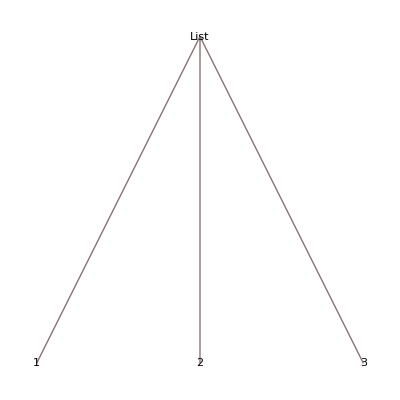

```mathematica
TreeForm[{1,2,3}]
```

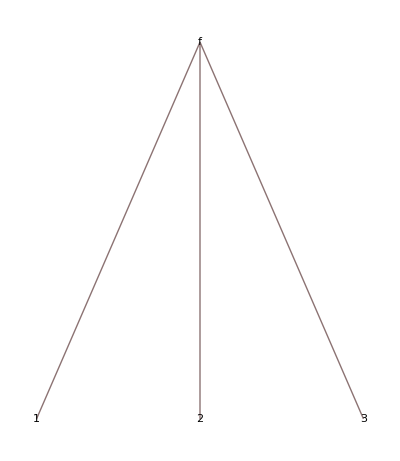

```mathematica
TreeForm[Apply[f,{1,2,3}]]
```

Apply changes the head of an expression

```mathematica
Head[{a,b,c,d}]
```

List

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
Head[%]
```

f

```mathematica
f@@{a,b,c,d} (*@@ is Apply, while /@ is Map*)
```

f[a,b,c,d]

```mathematica
{a,b,c,d}//FullForm
```

List[a,b,c,d]

```mathematica
a+b+c+d//FullForm
```

Plus[a,b,c,d]

```mathematica
Plus@@{a,b,c,d}
```

a+b+c+d

```mathematica
Plus@@Map[f,{a,b,c,d}]
```

f[a]+f[b]+f[c]+f[d]

```mathematica
Clear[f]
```

### Rule and RuleDelayed, Replace and ReplaceRepeated

```mathematica
?Rule
```

```mathematica
{a,b,c,d}/.a->b (*Rule: /.*)
```

{b,b,c,d}

```mathematica
{a,b,c,d}/.{a->b,b->c} (*Note that the order does not matter!!!*)
```

{b,c,c,d}

```mathematica
{a,b,c,d}//.{a->b,b->c} (*This continues to apply the rule until the expression stops changing, so here the order matters!*)
```

{c,c,c,d}

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.0217645,0.0217645,0.0217645,0.0217645}

```mathematica
{x,x,x,x}/.x:>RandomReal[] (*This is RuleDelayed!*) (*type : >*)
```

{0.62615,0.108003,0.735803,0.117765}

The difference between Rule and RuleDelayed is similar to the difference between Set ( = ) and SetDelayed ( := ).
   In the non - delayed case, the rhs is evaluated first and only after that the attribution (replacement) is performed. 
  In the delayed case, the attribution lhs := rhs is done first, and the evaluation is performed only when a value for lhs is provided.

```mathematica
factorial1[1]=1;
factorial1[n_]=n factorial1[n-1]
factorial1[4]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -1022+n.

Hold[n factorial1[-1+n]]

24

```mathematica
factorial2[1]=1;
factorial2[n_]:=n factorial2[n-1];
factorial2[4]
```

24

### Patterns

```mathematica
?_
```

_ or Blank[] is a pattern object that can stand for any Wolfram Language expression. 
_h or Blank[h] can stand for any expression with head h.

```mathematica
Clear[f];

f[x_]:=x^3-1
```

```mathematica
{f[2],f[y]}
```

{7,-1+y^3}

A function defined only for integer arguments

```mathematica
g[k_Integer]:= Prime[k]
```

```mathematica
{g[2],g[π]}
```

{3,g[π]}

```mathematica
?Prime
```

Prime[n] gives the n^th prime number.

```mathematica
earth = AstronomicalData["Earth","Image"]
```

-Graphics-

```mathematica
Clear[ls];

ls={4,3.14,17,"天高皇帝远",π,earth};
```

```mathematica
ls
```

{4,3.14,17,天高皇帝远,π,-Graphics-}

```mathematica
Head/@ls
```

{Integer,Real,Integer,String,Symbol,Image}

```mathematica
?Select
```

```mathematica
?Cases
```

```mathematica
Cases[ls,_]
```

{4,3.14,17,天高皇帝远,π,-Graphics-}

```mathematica
Cases[ls,_Symbol]
```

{π}

```mathematica
Cases[ls,_Image]
```

{-Graphics-}

```mathematica
Cases[ls, _String]
```

{天高皇帝远}

```mathematica
Cases[ls,_Integer]
```

{4,17}

```mathematica
Cases[ls,_?NumberQ]
```

{4,3.14,17}

```mathematica
Cases[ls, _?PrimeQ]
```

{17}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

All the squares less than 100

```mathematica
Cases[Range[100], _?(IntegerQ[ Sqrt[#]]&) ]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Select[Range[100], IntegerQ[ Sqrt[#]]&]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
22/7/.x_/y_-> {x,y} (*Recall Rules*)
```

22/7

The replacement did not work, because 22/7 and x/y are expressions with different structures. So check the FullForm before:

```mathematica
FullForm[x/y]
```

Times[x,Power[y,-1]]

```mathematica
FullForm[22]
```

22

```mathematica
22/7/.Rational[x_,y_]-> {x,y}
```

{22,7}

```mathematica
List @Rational[22,7]
```

{22/7}

```mathematica
2.34+2.09 ⅈ/.x_+ⅈ y_ -> {x,y}
```

2.34+2.09 ⅈ

```mathematica
FullForm[2.34+2.09 ⅈ]
```

Complex[2.34,2.09]

```mathematica
FullForm[x+ⅈ y]
```

Plus[x,Times[Complex[0,1],y]]

```mathematica
2.34+2.09 ⅈ/.Complex[x_,y_] -> {x,y}
```

{2.34,2.09}

```mathematica
2.34+2.09 ⅈ/.z_ -> {Re[z],Im[z]}
```

{2.34,2.09}

```mathematica
zsolns=NSolve[z^7-1==0]
```

{{z→-0.900969-0.433884 ⅈ},{z→-0.900969+0.433884 ⅈ},{z→-0.222521-0.974928 ⅈ},{z→-0.222521+0.974928 ⅈ},{z→0.62349-0.781831 ⅈ},{z→0.62349+0.781831 ⅈ},{z→1.}}

```mathematica
pts={Re[z],Im[z]}/.zsolns    (*This is good to remember!!!*)
```

{{-0.900969,-0.433884},{-0.900969,0.433884},{-0.222521,-0.974928},{-0.222521,0.974928},{0.62349,-0.781831},{0.62349,0.781831},{1.,0}}

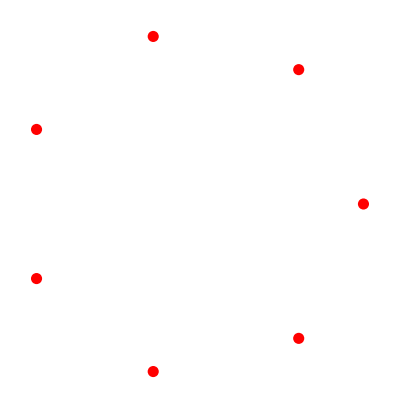

```mathematica
Graphics[{Red,AbsolutePointSize[8],Point[pts]},   
                    Axes-> Automatic]
```

Manipulating polynomials

### A cyclotomic polynomial

```mathematica
Factor[z^15-1] (*Over the integers*)
```

(-1+z) (1+z+z^2) (1+z+z^2+z^3+z^4) (1-z+z^3-z^4+z^5-z^7+z^8)

```mathematica
Φ[z_]:=1-z+z^3-z^4+z^5-z^7+z^8
```

```mathematica
G={1,2,4,7,8,11,13,14}; (*This is actually a group with multiplication mod 15*)
```

```mathematica
?PolynomialReduce
```

PolynomialReduce[poly,{poly_1,poly_2,…},{x_1,x_2,…}] yields a list representing a reduction of poly in terms of the poly_i. The list has the form {{a_1,a_2,…},b}, where b is minimal and a_1 poly_1+a_2 poly_2+…+b is exactly poly.

```mathematica
PolynomialRemainder[Φ[z^2],Φ[z],z]
```

0

```mathematica
PolynomialReduce[Φ[z^2],Φ[z],z]
```

{{1+z-z^3-z^4-z^5+z^7+z^8},0}

```mathematica
Table[PolynomialRemainder[Φ[z^g],Φ[z],z],{g,G}](*Nice construction*)
```

{0,0,0,0,0,0,0,0}

```mathematica
Solve[Φ[w]==0]
```

{{w→-(-1)^(1/15)},{w→(-1)^(2/15)},{w→(-1)^(4/15)},{w→-(-1)^(7/15)},{w→(-1)^(8/15)},{w→-(-1)^(11/15)},{w→-(-1)^(13/15)},{w→(-1)^(14/15)}}

```mathematica
Solve[Φ[w]==0]/. {(-1)^(1/15)->-z, (-1)^(j_/15)->(-1)^j z^j} (*This again doesn't work because of the different structures*)
```

{{w→z},{w→(-1)^(2/15)},{w→(-1)^(4/15)},{w→-(-1)^(7/15)},{w→(-1)^(8/15)},{w→-(-1)^(11/15)},{w→-(-1)^(13/15)},{w→(-1)^(14/15)}}

```mathematica
(-1)^(2/15)//FullForm
```

Power[-1,Rational[2,15]]

```mathematica
Solve[Φ[w]==0]/. {(-1)^(1/15)->-z, Power[-1,Rational[j_,15]]->(-1)^j z^j}
```

{{w→z},{w→z^2},{w→z^4},{w→z^7},{w→z^8},{w→z^11},{w→z^13},{w→z^14}}

### Groebner basis

Compute a Groebner basis - the idea of this is to find another set of simpler polynomials.

```mathematica
gb=GroebnerBasis[{x^2-2 y^2,x y-3},{x,y}]
```

{-9+2 y^4,3 x-2 y^3}

```mathematica
Solve[gb==0]
```

{{x→-2^(1/4) √3,y→-(√3)/2^(1/4)},{x→ⅈ 2^(1/4) √3,y→-(ⅈ √3)/2^(1/4)},{x→-ⅈ 2^(1/4) √3,y→(ⅈ √3)/2^(1/4)},{x→2^(1/4) √3,y→(√3)/2^(1/4)}}

```mathematica
Solve[{x^2-2 y^2,x y-3}==0]
```

{{x→-2^(1/4) √3,y→-(√3)/2^(1/4)},{x→-ⅈ 2^(1/4) √3,y→(ⅈ √3)/2^(1/4)},{x→ⅈ 2^(1/4) √3,y→-(ⅈ √3)/2^(1/4)},{x→2^(1/4) √3,y→(√3)/2^(1/4)}}

Prove that polynomials have no common roots:

```mathematica
GroebnerBasis[{x+y,x^2-1,y^2-2x},{x,y}]
```

{1}

```mathematica
NSolve[{x+y,x^2-1,y^2-2x}==0]
```

{}

```mathematica
polys={3 x^2+y z-5x-1, 2x+3 x y+y^2,x-3y+x z-2 z^2};
```

```mathematica
gb=GroebnerBasis[polys,{x,y,z}]
```

{-1772-710 z+3653 z^2+748 z^3+711 z^4+3064 z^5-314 z^6-896 z^7+72 z^8,2919537727088+42907663790334 y+3928775021139 z+28114074864208 z^2-54650967173 z^3+1797838568888 z^4-1818218283354 z^5-940700863552 z^6+85799291400 z^7,101977837394420+85815327580668 x-44563746052776 z-132499058173595 z^2+96518479090729 z^3-119620552893922 z^4-37331258048706 z^5+46653549404648 z^6-3431808123192 z^7}

```mathematica
Length[gb]
```

3

```mathematica
gb//Column
```

-1772-710 z+3653 z^2+748 z^3+711 z^4+3064 z^5-314 z^6-896 z^7+72 z^8
2919537727088+42907663790334 y+3928775021139 z+28114074864208 z^2-54650967173 z^3+1797838568888 z^4-1818218283354 z^5-940700863552 z^6+85799291400 z^7
101977837394420+85815327580668 x-44563746052776 z-132499058173595 z^2+96518479090729 z^3-119620552893922 z^4-37331258048706 z^5+46653549404648 z^6-3431808123192 z^7

```mathematica
Solve[gb⟦3⟧==0,x]
```

{{x→1/85815327580668(-101977837394420+44563746052776 z+132499058173595 z^2-96518479090729 z^3+119620552893922 z^4+37331258048706 z^5-46653549404648 z^6+3431808123192 z^7)}}

```mathematica
Solve[gb⟦2⟧==0,y]
```

{{y→1/42907663790334(-2919537727088-3928775021139 z-28114074864208 z^2+54650967173 z^3-1797838568888 z^4+1818218283354 z^5+940700863552 z^6-85799291400 z^7)}}

```mathematica
NSolve[gb⟦1⟧==0,z]
```

{{z→-1.59681},{z→-1.0629},{z→-0.718594},{z→0.281774-1.04636 ⅈ},{z→0.281774+1.04636 ⅈ},{z→0.658504},{z→2.08509},{z→12.5156}}

```mathematica
gb7=GroebnerBasis[polys,{x,y,z},Modulus->7]
```

{6+6 z+z^2+4 z^3+3 z^4+6 z^5+3 z^6+z^7,1+4 y+4 z+y z+4 z^3+z^4+z^6,1+3 y+y^2+6 z^2+3 z^3+3 z^4+3 z^5+4 z^6,1+x+y+3 z+2 z^2+2 z^3+6 z^4+z^5}

### Working with algebraic extensions

```mathematica
Clear[z]
```

```mathematica
M={{-1,5 z^3,5 z^2,-5z,-5 z^4,1},
  {4 z^2,5(z+z^4),5(z+z^2),0,0,z^2},
  {4 z^3,5(z^3+z^4),5(z+z^4),0,0,z^3},
  {-6 z^4,0,0,-5(z^2+z^3),-5(z^2+z^4),z^4},
  {-6z,0,0,-5(z+z^3),-5(z^2+z^3),z},
  {24,30 z^3,30 z^2,20z,20 z^4,1}};
```

```mathematica
M//MatrixForm
```

(-1 | 5 z^3 | 5 z^2 | -5 z | -5 z^4 | 1
4 z^2 | 5 (z+z^4) | 5 (z+z^2) | 0 | 0 | z^2
4 z^3 | 5 (z^3+z^4) | 5 (z+z^4) | 0 | 0 | z^3
-6 z^4 | 0 | 0 | -5 (z^2+z^3) | -5 (z^2+z^4) | z^4
-6 z | 0 | 0 | -5 (z+z^3) | -5 (z^2+z^3) | z
24 | 30 z^3 | 30 z^2 | 20 z | 20 z^4 | 1)

```mathematica
p=Collect[
CharacteristicPolynomial[M,λ],λ,Simplify]
```

15625 (-1+z)^5 z^5 (-1-2 z+z^2+15 z^3+50 z^4+93 z^5+122 z^6+114 z^7+70 z^8+30 z^9+8 z^10)+6250 z^4 (-2+2 z+2 z^2+5 z^3+5 z^4-15 z^5-4 z^6-19 z^7+20 z^8+20 z^9-9 z^10+2 z^11-8 z^12+z^15) λ-625 (-1+z)^2 z^2 (1-3 z-9 z^2-10 z^3-10 z^4+3 z^6+4 z^7+15 z^8+20 z^9+9 z^10+5 z^11) λ^2+250 (-1+z)^2 z (1+z+3 z^3+6 z^4+15 z^5+15 z^6+6 z^7+3 z^8) λ^3+25 (-1+z^2-5 z^3-4 z^4-8 z^5-4 z^6-5 z^7+z^8) λ^4-10 (-1+z)^2 z (1+z) λ^5+λ^6

```mathematica
cpoly=
Collect[
CharacteristicPolynomial[M,λ],λ,Simplify[PolynomialRemainder[#,1+z+z^2+z^3+z^4,z]]&]
```

1953125+156250 (1+2 z^2+2 z^3) λ-15625 λ^2-2500 (1+2 z^2+2 z^3) λ^3-125 λ^4+10 (1+2 z^2+2 z^3) λ^5+λ^6

```mathematica
(1+2 z^2+2 z^3)/.z->ⅇ^(2π ⅈ/5)//FullSimplify
```

-√5

```mathematica
(1+2 z^2+2 z^3)/.z->ⅇ^(4π ⅈ/5) //FullSimplify
```

√5

```mathematica
cpoly1=Collect[cpoly/.z->ⅇ^(2π ⅈ/5),λ,FullSimplify]
```

1953125-156250 √5 λ-15625 λ^2+2500 √5 λ^3-125 λ^4-10 √5 λ^5+λ^6

```mathematica
Factor[cpoly1,Extension->√5]
```

(5 √5-λ)^4 (5 √5+λ)^2

```mathematica
cpoly2=Collect[cpoly/.z->ⅇ^(4π ⅈ/5),λ,FullSimplify]
```

1953125+156250 √5 λ-15625 λ^2-2500 √5 λ^3-125 λ^4+10 √5 λ^5+λ^6

Notice that √5 has changed sign

```mathematica
Factor[cpoly2,Extension->√5]
```

(5 √5-λ)^2 (5 √5+λ)^4

So the characteristic polynomial looks as if it is

```mathematica
p=(λ+5(1+2 z^2+2 z^3))^4 (λ-5(1+2 z^2+2 z^3))^2;
```

```mathematica
Collect[p,λ,Simplify[PolynomialRemainder[#,1+z+z^2+z^3+z^4,z]]&]
```

1953125+156250 (1+2 z^2+2 z^3) λ-15625 λ^2-2500 (1+2 z^2+2 z^3) λ^3-125 λ^4+10 (1+2 z^2+2 z^3) λ^5+λ^6

```mathematica
%-cpoly
```

0

Simple Programs

### Nest

```mathematica
NestList[1/2(#+2/#)&,2.,10] (*Recall from lecture 1 the Newton iteration*)
```

{2.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421}

```mathematica
?Nest
```

Nest[f,expr,n] gives an expression with f applied n times to expr.

```mathematica
NestList[1/2(#+2/#)&,2,10]
```

{2,3/2,17/12,577/408,665857/470832,886731088897/627013566048,1572584048032918633353217/1111984844349868137938112,4946041176255201878775086487573351061418968498177/3497379255757941172020851852070562919437964212608,48926646634423881954586808839856694558492182258668537145547700898547222910968507268117381704646657/34596363615919099765318545389014861517389860071988342648187104766246565694525469768325292176831232,4787633501779563550338751478164352626393810985192405254654229276251925362787770306352384325384596398594331240032637710299217577668263130246892221798809427255174348445597103634783814035090442551297/3385368114944226131160489088412764413184597197600430424080424489217455640335520865446091847042392283395113030493175270757327077204943610618917073241080260452775055121081948254768847591544963982848,45842869094724092282256664559525216692173091162526497018856817207453767127095354052418072639857700888691134361639497243771528176716782876457748796945284249594870200383920805322146999777923783319507727283850422831309915607777814766948159289963355518294865659883896712136501856004613518112550490551045680741845733583765205748593300762225277706242970719821414680060203467479543923750220952764417/32415803605926610717906209990215925889160576452720547724429585547651493040781333832362975891811042370960101005436793459936444123023843707180863927766463725709098731479142615931281199106042945274354413006295825020803450451201071934075872286636802447240751072096022370680513420925571815159954608073162324835009657121509219599603167122882578517323407726312472428238351392267283960361495336307712}

```mathematica
?FixedPoint
```

FixedPoint[f,expr] starts with expr, then applies f repeatedly until the result no longer changes.

```mathematica
FixedPoint[1/2(#+2/#)&,2.]
```

1.41421

```mathematica
N[2,50]
```

2.

```mathematica
FixedPoint[1/2(#+2/#)&,N[2,50]]
```

1.4142135623730950488016887242096980785696718753769

### The Newton iteration again

We have a program based on iteration

```mathematica
root[init_,acc_]:=
Module[{x=init,y=init+1},
              While[Abs[x-y]>10^(-(acc+1)),
                         y=x;
                         x=N[x-f[x]/f'[x],acc+1]];
              x  ]
```

Nest is a function that maps a function repeatedly

```mathematica
Nest[g,x,4]
```

g[g[g[g[x]]]]

What we need is NestWhile

```mathematica
?NestWhile
```

NestWhile[f,expr,test] starts with expr, then repeatedly applies f until applying test to the result no longer yields True. 
NestWhile[f,expr,test,m] supplies the most recent m results as arguments for test at each step. 
NestWhile[f,expr,test,All] supplies all results so far as arguments for test at each step. 
NestWhile[f,expr,test,m,max] applies f at most max times. 
NestWhile[f,expr,test,m,max,n] applies f an extra n times. 
NestWhile[f,expr,test,m,max,-n] returns the result found when f had been applied n fewer times.

```mathematica
Clear[f];

f[x_]:=x^2-2

update[{x_,y_},acc_]:={N[x-f[x]/f'[x],acc+1],x}
```

```mathematica
root1[init_,acc_]:=
NestWhile[update[#,acc]&,{init,init+1},Abs[#⟦1⟧-#⟦2⟧]>10^(-acc-1)&]⟦1⟧
```

```mathematica
root1[2,100]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276416

Now we incorporate this in to a routine that finds a root of a general function.  We also introduce g[x] = ∂_x f[x], to avoid recomputing the derivative with each iteration.

```mathematica
Clear[g]
```

```mathematica
findroot[fn_,init_, acc_]:=
Module[{x=init,y=init+1},
g[x_]:=fn'[x];(*so we don't calculate the derivative everytime we run around the loop*)
update[{x_,y_}]:={N[x-fn[x]/g[x],acc+5],x};
NestWhile[update[#]&,{init,init+1},Abs[#⟦1⟧-#⟦2⟧]>10^(-acc-5)&]⟦1⟧
              ]
```

```mathematica
f[x_]:=x^3-2
```

```mathematica
findroot[f,2,100]
```

1.25992104989487316476721060727822835057025146470150798008197511215529967651395948372939656243625509415

```mathematica
%^3-2
```

0.